# Dirac Delta NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## definitions and derivations

```mathematica
Dirac`D[u_,ud_]:=DiracDelta[u-ud]/(2 Pi ud)
```

```mathematica
Dirac`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

```mathematica
Dirac`Λ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]/u-1
```

```mathematica
(1+Dirac`Λ[u,ud])u==Dirac`σ[u,ud]
```

True

```mathematica
FullSimplify[(Dirac`Λ[u,ud])u==Dirac`σ[-u,ud],Assumptions->0<ud<1&&-1<u<1]
```

2 π u ud==u

### height field normalization

```mathematica
Integrate[2Pi u Dirac`D[u,ud],{u,0,1},Assumptions->0<ud<1]
```

1

### distribution of slopes

```mathematica
Dirac`P22[p_,q_,ud_]:=DiracDelta[1/(√(1+p^2+q^2))-ud]/(2 π (1+p^2+q^2)^2 ud)
```

```mathematica
Integrate[Dirac`P22[p,q,ud],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<ud<1]
```

1

```mathematica
Dirac`P2[q_,ud_]:=ud/(2 π √Abs[-1+(1+q^2) ud^2])HeavisideTheta[(-1-q^2+1/ud^2)]
```

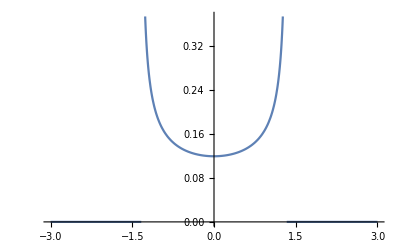

```mathematica
Plot[{Dirac`P2[q,.6]},{q,-3,3}]
```